```mathematica
f[x_]:=Piecewise[{{1/x^(5/2),x≥1},{1/(-x)^(5/2),x≤-1}}]
```

```mathematica
Integrate[f[x],{x,-Infinity,Infinity}]
```

4/3

```mathematica
g[x_]=f[x]/Integrate[f[y],{y,-Infinity,Infinity}]
```

3/4 (Piecewise[{{1/x^(5/2), x≥1}, {1/(-x)^(5/2), x≤-1}, {0, True}}])

```mathematica
g[3]
```

1/(12 √3)

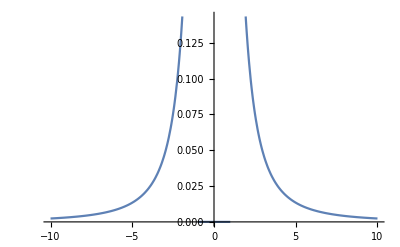

```mathematica
Plot[g[x],{x,-10,10}]
```

```mathematica
d:=ProbabilityDistribution[g[x],{x,-Infinity,Infinity}]
```

```mathematica
Mean[d]
```

0

```mathematica
RandomVariate[d,{2,10}]
```

{{-1.98407,-1.49812,1.3572,5.92369,1.29874,-1.45307,1.60484,3.07393,2.43468,1.12946},{-1.19703,-1.42181,2.98936,1.74216,7.74445,-1.90754,1.02463,-1.64802,-6.26271,-2.28174}}

```mathematica
mat[s_]:=Plus @@Map[(Outer[Times,#,#])&,RandomVariate[d,{s,10}]]/s
```

```mathematica
mat[s_]:=Plus @@Map[(Outer[Times,#,#])&,RandomVariate[NormalDistribution[],{s,10}]]/s
```

```mathematica
cov=With[{m=mat[20000]},Transpose[m].m]
```

{{8006.13,100.57,50.5432,117.731,-20.4788,-47.8055,72.2341,-80.8516,-2.46891,161.204},{100.57,6063.78,373.727,-90.8572,43.8804,62.0505,13.2192,80.4827,173.335,67.7033},{50.5432,373.727,30522.7,8.14405,71.2607,8.48841,59.063,-27.0196,767.603,-60.0481},{117.731,-90.8572,8.14405,12043.3,35.6777,10.6746,23.9497,-175.946,-207.7,5.28121},{-20.4788,43.8804,71.2607,35.6777,5780.33,8.25104,3.92521,116.598,173.011,59.493},{-47.8055,62.0505,8.48841,10.6746,8.25104,37780.9,72.7946,-36.9572,174.576,-239.564},{72.2341,13.2192,59.063,23.9497,3.92521,72.7946,5584.12,93.1811,-186.341,-9.55265},{-80.8516,80.4827,-27.0196,-175.946,116.598,-36.9572,93.1811,35699.8,110.381,96.6105},{-2.46891,173.335,767.603,-207.7,173.011,174.576,-186.341,110.381,53146.8,29.4846},{161.204,67.7033,-60.0481,5.28121,59.493,-239.564,-9.55265,96.6105,29.4846,17738.5}}

```mathematica
cov=mat[200]
```

{{1392.47,7.1945,7.09406,-4.85265,-3.09783,6.72102,-1.1056,5.81025,-5.29251,-5.41387},{7.1945,19.0033,0.593562,-6.5526,0.0377427,-3.27744,-0.280028,0.123573,0.532718,0.0431242},{7.09406,0.593562,70.3924,7.26259,-1.12751,9.60701,0.166758,0.23395,0.971433,-2.17061},{-4.85265,-6.5526,7.26259,4013.87,5.95418,-8.31354,-10.897,8.92778,-4.67367,3.966},{-3.09783,0.0377427,-1.12751,5.95418,30.0135,2.73509,2.03889,0.402846,3.16455,-3.90093},{6.72102,-3.27744,9.60701,-8.31354,2.73509,1069.4,16.0764,-49.5732,10.4191,-1.94575},{-1.1056,-0.280028,0.166758,-10.897,2.03889,16.0764,356.436,-0.694034,-7.88049,-0.112659},{5.81025,0.123573,0.23395,8.92778,0.402846,-49.5732,-0.694034,11.1602,-0.477684,0.055088},{-5.29251,0.532718,0.971433,-4.67367,3.16455,10.4191,-7.88049,-0.477684,12.7886,-0.55795},{-5.41387,0.0431242,-2.17061,3.966,-3.90093,-1.94575,-0.112659,0.055088,-0.55795,29.3143}}

```mathematica
Eigenvectors[cov]
```

{{0.00185316,0.00164073,-0.00182973,-0.999982,-0.00149023,0.00287753,0.00298824,-0.00226414,0.0011662,-0.00099702},{-0.999743,-0.0051799,-0.00552883,-0.00190194,0.00222555,-0.0201565,0.00075269,-0.0034957,0.00368306,0.00399354},{0.0199542,0.00326304,-0.00945601,-0.00299495,-0.00274834,-0.998349,-0.02236,0.0467476,-0.00977661,0.00178801},{0.0011176,-0.000683843,-0.000160595,0.00288531,0.00587895,-0.0220964,0.999454,0.00129678,-0.0236077,-0.000225067},{-0.00562108,0.011673,0.998216,-0.00176657,-0.0221904,-0.00921555,0.000437084,0.0105356,0.0150467,-0.0497926},{0.000343313,-0.00483157,0.0176165,0.000342826,-0.753111,0.00349921,0.00165141,-0.016389,-0.127876,0.644867},{0.00442774,0.0294191,0.0496675,-0.00164455,0.632284,-0.000869327,-0.000646578,0.0209873,0.1236,0.762328},{0.00499985,-0.996498,0.0144136,-0.00183778,0.0353422,-0.0022593,-0.00262318,0.00716704,-0.0711519,0.0195048},{-0.00397523,0.0768306,0.0181443,-0.00140999,0.174432,0.0105235,-0.0239206,0.017949,-0.98093,0.00973725},{-0.00442495,0.0047854,-0.0112999,-0.00204073,-0.0286866,0.0467146,0.000243196,0.9983,0.013795,-0.00530106}}

## No first moment

```mathematica
exponents:=Table[x,{x,11/10,19/10,1/10}]
```

```mathematica
n:=Length[exponents]
```

```mathematica
densities=Table[1/(1+Abs[x]^y)/Integrate[1/(1+Abs[x]^y),{x,-Infinity,Infinity}],{y,exponents}]
```

{(11 Sin[π/11])/(20 π (1+Abs[x]^(11/10))),3/(10 π (1+Abs[x]^(6/5))),(13 Sin[(3 π)/13])/(20 π (1+Abs[x]^(13/10))),(7 Cos[(3 π)/14])/(10 π (1+Abs[x]^(7/5))),(3 √3)/(8 π (1+Abs[x]^(3/2))),(4 Cos[π/8])/(5 π (1+Abs[x]^(8/5))),(17 Cos[(3 π)/34])/(20 π (1+Abs[x]^(17/10))),(9 Cos[π/18])/(10 π (1+Abs[x]^(9/5))),(19 Cos[π/38])/(20 π (1+Abs[x]^(19/10)))}

```mathematica
distributions=Table[ProbabilityDistribution[d,{x,-Infinity,Infinity}],{d,densities}]
```

{ProbabilityDistribution[(11 Sin[π/11])/(20 π (1+Abs[x]^(11/10))),{x,-∞,∞}],ProbabilityDistribution[3/(10 π (1+Abs[x]^(6/5))),{x,-∞,∞}],ProbabilityDistribution[(13 Sin[(3 π)/13])/(20 π (1+Abs[x]^(13/10))),{x,-∞,∞}],ProbabilityDistribution[(7 Cos[(3 π)/14])/(10 π (1+Abs[x]^(7/5))),{x,-∞,∞}],ProbabilityDistribution[(3 √3)/(8 π (1+Abs[x]^(3/2))),{x,-∞,∞}],ProbabilityDistribution[(4 Cos[π/8])/(5 π (1+Abs[x]^(8/5))),{x,-∞,∞}],ProbabilityDistribution[(17 Cos[(3 π)/34])/(20 π (1+Abs[x]^(17/10))),{x,-∞,∞}],ProbabilityDistribution[(9 Cos[π/18])/(10 π (1+Abs[x]^(9/5))),{x,-∞,∞}],ProbabilityDistribution[(19 Cos[π/38])/(20 π (1+Abs[x]^(19/10))),{x,-∞,∞}]}

```mathematica
Mean[distributions[[1]]]
```

$Aborted

```mathematica
RandomVariate[distributions[[9]],{2,10}]
```

{{0.644887,-4.23688,-0.594382,2.65062,10.0504,-1.03972,-0.525585,-2.83306,-0.838184,-0.323403},{-3.39323,0.227381,-1.3975,-3.64647,-1.95499,3.75243,2.62726,-5.10343,4.62206,-0.838664}}

```mathematica
randomvector:=Table[RandomVariate[d],{d,distributions}]
```

```mathematica
randomvectors[s_]:=Table[RandomVariate[d,s],{d,distributions}]//Transpose
```

```mathematica
outerproduct[v_]:=Outer[Times,v,v]
```

```mathematica
cov[s_]:=Mean[Table[
outerproduct[r]
,{r,randomvectors[s]}]]
```

```mathematica
cov[100]//MatrixForm
```

(1.82325×10^19 | -1.62843×10^13 | -2.02661×10^11 | -5.35113×10^9 | 3.45054×10^10 | 1.59401×10^9 | 4.83672×10^9 | -1.47662×10^11 | 3.0549×10^8
-1.62843×10^13 | 1.73114×10^13 | 8.10903×10^7 | 2.38155×10^6 | 966542. | 305147. | -541972. | 261731. | 1.71053×10^6
-2.02661×10^11 | 8.10903×10^7 | 2.90486×10^9 | -243251. | 197250. | -11738.2 | -135396. | -48867.5 | -9732.2
-5.35113×10^9 | 2.38155×10^6 | -243251. | 3.64648×10^11 | 9563.21 | 4745.6 | -91638.9 | 267482. | -40173.6
3.45054×10^10 | 966542. | 197250. | 9563.21 | 2.03382×10^6 | 80.5025 | 976.388 | 597.539 | -2369.36
1.59401×10^9 | 305147. | -11738.2 | 4745.6 | 80.5025 | 1251.24 | -15.8575 | 23.6827 | 8.3381
4.83672×10^9 | -541972. | -135396. | -91638.9 | 976.388 | -15.8575 | 3305.93 | -3.77537 | -24.0769
-1.47662×10^11 | 261731. | -48867.5 | 267482. | 597.539 | 23.6827 | -3.77537 | 2078.26 | -0.0586322
3.0549×10^8 | 1.71053×10^6 | -9732.2 | -40173.6 | -2369.36 | 8.3381 | -24.0769 | -0.0586322 | 51.6572)

```mathematica
Eigenvectors[%]
```

{{1.,-8.93148×10^-7,-1.11154×10^-8,-2.93495×10^-10,1.89253×10^-9,8.74271×10^-11,2.65281×10^-10,-8.09883×10^-9,1.67553×10^-11},{8.93148×10^-7,1.,4.67455×10^-6,1.4025×10^-7,5.76131×10^-8,1.77092×10^-8,-3.10578×10^-8,7.50174×10^-9,9.88252×10^-8},{2.93368×10^-10,-1.40247×10^-7,-6.72636×10^-7,1.,2.6253×10^-8,1.30154×10^-8,-2.51304×10^-7,7.33415×10^-7,-1.10171×10^-7},{-1.1111×10^-8,4.67456×10^-6,-1.,-6.72635×10^-7,-0.0000680814,4.03528×10^-6,0.0000465907,0.0000173878,3.35197×10^-6},{1.88992×10^-9,5.71688×10^-8,0.0000680551,2.66258×10^-8,-0.999999,-0.000041445,-0.000482358,-0.000435392,0.00116506},{-1.28096×10^-9,3.65511×10^-8,0.0000398827,3.34439×10^-7,-0.000389371,-0.332499,0.933876,-0.131334,-0.00847442},{-4.93559×10^-9,6.74224×10^-9,-0.000029523,3.8469×10^-7,0.000465443,-0.701097,-0.337925,-0.627909,0.},{6.29946×10^-9,1.7809×10^-9,5.3729×10^-6,-5.83729×10^-7,-0.000251562,-0.630793,-0.116706,0.767124,0.},{-2.98647×10^-11,-9.86014×10^-8,3.61079×10^-6,1.12981×10^-7,0.0011618,-0.00281779,0.0079149,-0.00111251,0.999963}}